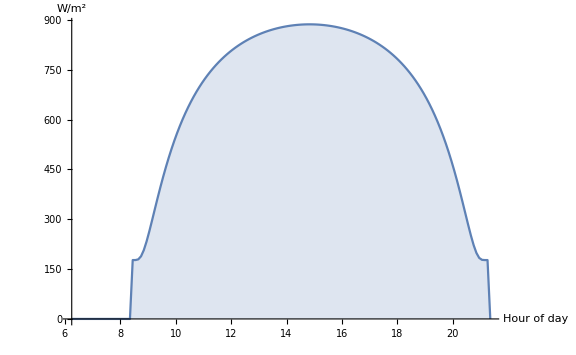

```mathematica
angle:= Function[ (* params: hour of day, solar panel angle, date, returns misalignment with the sun in radians *)
sunPos = SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[#3,{#1}]];
(* remove degree unit, then convert to radians *)
Subscript[γ, s]= QuantityMagnitude[Quantity[sunPos[[1]]]]*Pi/180;  (* Azimuth of sun position, 0 due South, negative to the east *)
(* Because Mathematica gives azimuth in compass angle, we subtract 180 degrees *)
Subscript[γ, s] = Subscript[γ, s] - Pi;
Subscript[θ, s]= QuantityMagnitude[Quantity[sunPos[[2]]]]*Pi/180; (* Sun altitude *)
Subscript[γ, p] = 0 * Pi/180; (* Solar panels azimuth *)
Subscript[θ, p] = #2 * Pi/180; (* Solar panels angle with horizontal *)
a= ArcCos[Cos[Subscript[γ, p]-Subscript[γ, s]] Cos[Subscript[θ, s]] Sin[Subscript[θ, p]]+Cos[Subscript[θ, p]] Sin[Subscript[θ, s]]]
]

date  = DateObject[{2016,8,6}];
n= QuantityMagnitude[Quantity[date - DateObject[{2016,1,1}]]];
Subscript[I, 0]= 1367 (1+0.034 Cos[360*n/365.25]);
position = GeoPosition[{51.546545,4.411744}];
sunrise = TimeZoneConvert[Sunrise[position,date],2];
Subscript[t, sunrise] = N[DateValue[sunrise,"Hour"]+DateValue[sunrise, "Minute"]/60];
sunset = TimeZoneConvert[Sunset[position,date],2];
Subscript[t, sunset] = N[DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60];

simplePower := Function[
(* simple model *)
(* day of year *)
Subscript[I, noon] = 1000; (* peak, noontime solar irradiance level *)
t = 17; (* time in hours *)
(* simple version, uses Subscript[I, noon] *)
Subscript[I, si]= N[Subscript[I, noon] Sin[180 (t - Subscript[t, sunrise])/(Subscript[t, sunset]-Subscript[t, sunrise]) Pi/180]] 
(*convert to radians*)
]

directPower  := Function [ (* param: hour of day *)
Subscript[θ, z]=angle[#1,30,date]; (* solar zenith (misalignment) in radians *)
Subscript[a, 0] = 0.4237 - 0.00821 36;
Subscript[a, 1] = 0.5055 + 0.00595 6.5^2;
k = 0.2711 + 0.01858 2.5^2;
If[Cos[Subscript[θ, z]]<0,
Subscript[I, direct]=0,
Subscript[I, direct] = Subscript[I, 0] (Subscript[a, 0] + Subscript[a, 1] E^(-k/Cos[Subscript[θ, z]])) (* If the sun is more than 90 degrees off, the formula is not correct, and we set the value to be 0 *)
]
]


DiscretePlot[directPower[x],{x,Subscript[t, sunrise],Subscript[t, sunset],0.1},ImageSize->Large,AxesLabel -> {"Hour of day", "W/m^2"}]
```